```mathematica
<<Local`QFTToolKit`
QCDBaseIndices
Put[SaveFile=NBname["stub"]<>".out"]
```

{{0,1,2,3},{field,{1,2,3,4}},{feyn,{1,2,3,4,5}},{space,{1,2,3}},{timespace,{0,1}},{groupR,{1,2,3}},{gaugeG,{1,2,3,4,5,6,7,8}},{color,{1,2,3}},{flavor,{1,2,3,4,5,6}},{family,{1,2,3}}}

```mathematica
DefineTensorShortcuts[{{η,t,δ,ε,λ,D,F,U,H,g,τ,v,H,m,μ,Q},1},
{{T},2},
{{σ,λ,T},3},
{{σ},4}
]
```

VIII.3 Effective Field Theory

```mathematica
PR1["VIII.2.1.  Consider ",tmpL=ℒ->1/2(xPartialD[φd[1],μ]^2+xPartialD[φd[2],μ]^2)-λ(φd[1]^4+φd[2]^4)-g φd[1]^2φd[2]^2," We have taken the O[2] theory from chapter I.10 and broken the symmetry explicitly.  Work out the renormalization group flow in the (λ-g) plane and draw your own conclusions."
]
```

VIII.2.1.  Consider ℒ→-g (φ_1^1)^2 (φ_2^2)^2-λ ((φ_1^1)^4+(φ_2^2)^4)+1/2 ((UnderBar[∂]_μ[φ_1^1])^2+(UnderBar[∂]_μ[φ_2^2])^2) We have taken the O[2] theory from chapter I.10 and broken the symmetry explicitly.  Work out the renormalization group flow in the (λ-g) plane and draw your own conclusions.

General graphic definitions for array points and lines.

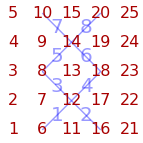

```mathematica
{vx,line}=GraphicPointLines[5,5,{{6,12},{16,12},{12,8},{12,18},{8,14},{18,14},{14,10},{14,20}}];
```

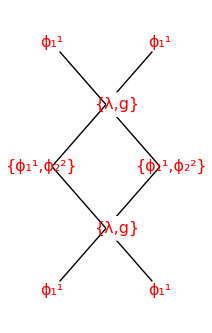

```mathematica
Graphics[{Thin,Black,Map[Line[#]&,line],
TextOver[ϕd[1],vx[[16]]],
TextOver[ϕd[1],vx[[6]]],
TextOver[ϕd[1],vx[[10]]],
TextOver[ϕd[1],vx[[20]]],
TextOver[{ϕd[1],ϕd[2]},vx[[8]]+{-.2,0}],
TextOver[{ϕd[1],ϕd[2]},vx[[18]]+{.2,0}],
TextOver[{λ,g},vx[[12]]+{.2,0}],
TextOver[{λ,g},vx[[14]]+{.2,0}]
}
]
```